# Mosquito population dynamics include Early instars, layter instars, pupae, and adults female.

## How to use

Using the code here we can determine seasonal patterns in infection and test the effect of IRS on the mosquito populations. This is a deterministic implementation of the model by White et al. 2011, which itself relies on other references and particularly Griffin et al. 2010. The workflow is to feed the function here the seasonal and/or IRS scheme that we want, and to take the output and feed it to the parameter file of the ABM.

White MT, Griffin JT, Churcher TS, Ferguson NM, Basáñez M-G, Ghani AC. Modelling the impact of vector control interventions on Anopheles gambiae population dynamics. Parasit Vectors. 2011;4: 153.

```mathematica
ClearAll[A,P,L,M,K,f,MuM,MuE,MuL, c, TimeMax];
```

## Carrying capacity

(* 
Carrying capacity is just for the first 2 stages (denoted "A" in the ODE model below), as their mortality rates depend on carrying capacity. It is just a sinus function (this is not from the paper). The width (frequency) is matched to the length of the rainy season. What is different between the Seasonality sub-sections below is the values of FirstDayOfRain, LastDayOfRain, the multipliers of the sinus function and the baseline number of mosquitoes
*)

```mathematica
Seasonality 1
```

```mathematica
FirstDayOfRain=160; (* running day in a year of 360 days where each month is exactly 30 days. For example, 180 will be 30 of June *)
LastDayOfRain=270; (* running day in a year of 360 days where each month is exactly 30 days. For example, 180 will be 30 of June *)
Muliplier1=0.5;
Muliplier2=0.5;
BaseLine=100;
phase=LastDayOfRain- FirstDayOfRain; (*This is the length of the rainy season*)
peakShift=phase*3/4-FirstDayOfRain ; (*This shifts the peak of the sin function towards where peak of rainy season should be.*)
K[t_]:=10000*(Muliplier1+Muliplier2*Sin[2π*(t/phase+peakShift/phase)]); (*Division by phase is to match the phase of the sin function to the seasonality; The value of the sin function is -1 to 1 so its multiplication by 0.5 and the addition of 0.5 is to define a minimum (positive) and a maximum value for the number of mosquitos. The 10000 is just an arbitrary number. *)
f[t_]:=Piecewise[{{K[Mod[t,360]],FirstDayOfRain<Mod[t,360]<LastDayOfRain}},BaseLine];  (*Seasonality in carrying capacity. In the rainy season, calculate K. Otherwise set to a baseline of 100 *)
Plot[K[t],{t,0,360}]
Plot[f[t],{t,0,360}]
```

```mathematica
Seasonality 2
```

```mathematica
FirstDayOfRain=145; (* running day in a year of 360 days where each month is exactly 30 days. For example, 180 will be 30 of June *)
LastDayOfRain=270; (* running day in a year of 360 days where each month is exactly 30 days. For example, 180 will be 30 of June *)
Muliplier1=0.5;
Muliplier2=0.5;
BaseLine=100;
phase=LastDayOfRain- FirstDayOfRain; (*This is the length of the rainy season*)
peakShift=phase*3/4-FirstDayOfRain ; (*This shifts the peak of the sin function towards where peak of rainy season should be.*)
K[t_]:=10000*(Muliplier1+Muliplier2*Sin[2π*(t/phase+peakShift/phase)]); (*Division by phase is to match the phase of the sin function to the seasonality; The value of the sin function is -1 to 1 so its multiplication by 0.5 and the addition of 0.5 is to define a minimum (positive) and a maximum value for the number of mosquitos. The 10000 is just an arbitrary number. *)
f[t_]:=Piecewise[{{K[Mod[t,360]],FirstDayOfRain<Mod[t,360]<LastDayOfRain}},BaseLine];  (*Seasonality in carrying capacity. In the rainy season, calculate K. Otherwise set to a baseline of 100 *)
Plot[K[t],{t,0,360}]
Plot[f[t],{t,0,360}]
```

```mathematica
Seasonality 3
```

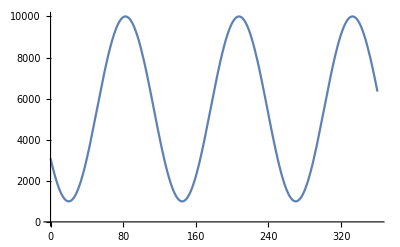

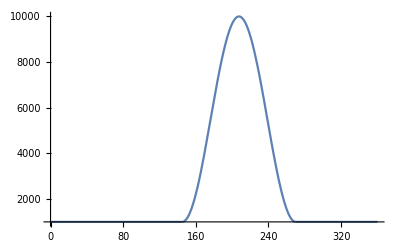

```mathematica
FirstDayOfRain=145; (* running day in a year of 360 days where each month is exactly 30 days. For example, 180 will be 30 of June *)
LastDayOfRain=270; (* running day in a year of 360 days where each month is exactly 30 days. For example, 180 will be 30 of June *)
Muliplier1=0.55;
Muliplier2=0.45;
BaseLine=1000;
phase=LastDayOfRain- FirstDayOfRain; (*This is the length of the rainy season*)
peakShift=phase*3/4-FirstDayOfRain ; (*This shifts the peak of the sin function towards where peak of rainy season should be.*)
K[t_]:=10000*(Muliplier1+Muliplier2*Sin[2π*(t/phase+peakShift/phase)]); (*Division by phase is to match the phase of the sin function to the seasonality; The value of the sin function is -1 to 1 so its multiplication by 0.5 and the addition of 0.5 is to define a minimum (positive) and a maximum value for the number of mosquitos. The 10000 is just an arbitrary number. *)
f[t_]:=Piecewise[{{K[Mod[t,360]],FirstDayOfRain<Mod[t,360]<LastDayOfRain}},BaseLine];  (*Seasonality in carrying capacity. In the rainy season, calculate K. Otherwise set to a baseline of 100 *)
Plot[K[t],{t,0,360}]
Plot[f[t],{t,0,360}]
```

```mathematica
Seasonality 4 (used for the PLOS Biol paper)
```

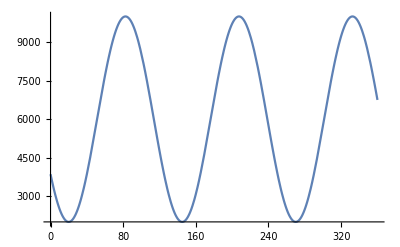

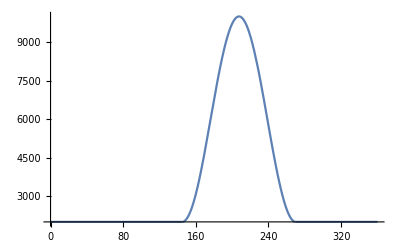

```mathematica
FirstDayOfRain=145; (* running day in a year of 360 days where each month is exactly 30 days. For example, 180 will be 30 of June *)
LastDayOfRain=270;(* running day in a year of 360 days where each month is exactly 30 days. For example, 180 will be 30 of June *)
Muliplier1=0.6;
Muliplier2=0.4;
BaseLine=2000;
phase=LastDayOfRain- FirstDayOfRain; (*This is the length of the rainy season*)
peakShift=phase*3/4-FirstDayOfRain ; (*This shifts the peak of the sin function towards where peak of rainy season should be.*)
K[t_]:=10000*(Muliplier1+Muliplier2*Sin[2π*(t/phase+peakShift/phase)]); (*Division by phase is to match the phase of the sin function to the seasonality; The value of the sin function is -1 to 1 so its multiplication by 0.5 and the addition of 0.5 is to define a minimum (positive) and a maximum value for the number of mosquitos. The 10000 is just an arbitrary number. *)
f[t_]:=Piecewise[{{K[Mod[t,360]],FirstDayOfRain<Mod[t,360]<LastDayOfRain}},BaseLine];  (*Seasonality in carrying capacity. In the rainy season, calculate K. Otherwise set to a baseline of 100 *)
Plot[K[t],{t,0,360}]
Plot[f[t],{t,0,360}]
```

## Mortality rates

### Non - adult mortality rates

(* 
MuE and MuL are the daily mortality of eggs+early larvae and of late larva stages, respectively.  Both are density-dependent on the number of early and late larva stages, calculated as (A+L)/f, where f is the environmental carrying capacity at time t; 
\mu_E^0 and \mu_L^0 are assumed to be 0.035 and γ = 13.25. These values are taken from Table 1 in White et al 2011. The equations are Eq. 7 in the paper.
*)

```mathematica
MuE[t_]:=0.035*(1+(A[t]+L[t])/f[t]); 
MuL[t_]:=0.035*(1+13.25*(A[t]+L[t])/f[t]);
```

### Adult mortality rates -- this is the definition of the intervention

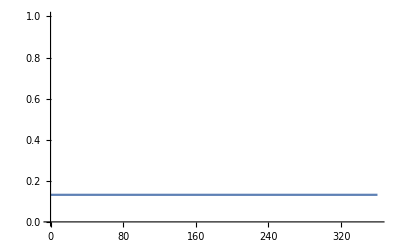

0.9

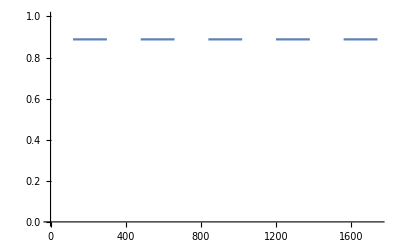

```mathematica
w[c_,Q_,ϕ_,r_,ψ_]:=1-Q*c*ϕ*(1-(1-r)(1-ψ)); (* A function indicating how IRS cahnges the adult mortatlity rate. c is coverge and it is the only parameter here we should change. Parameters and their values are taken from Table S3 in the supplementary information *)

(*MuM is the daily mortality rate of adult mosquitos.The Log turns the w into a rate.*)

(* Example 0: No external mortality rates (no IRS), so c=0 *)
c=0;
TimeMax=360;
MuM [c_,Q_,ϕ_,r_,ψ_,t_]:= {-Log[0.91*w[c,Q,ϕ,r,ψ]*0.74/1-Q *c* ϕ* r*0.74]/3,0<t<TimeMax};
Plot[Evaluate[MuM[0,0.92,0.97,0.207,0.86,t]],{t,0,TimeMax},PlotRange->{0,1}]

(* Example 1: IRS of 3 months, May-July, with c=0.9, for 5 years *)
c=0.9
TimeMax=5*360;
MuM [c_,Q_,ϕ_,r_,ψ_,t_]:= Piecewise[{{-Log[0.91*w[c,Q,ϕ,r,ψ]*0.74/1-Q *c* ϕ* r*0.74]/3,120<Mod[t,360]<300}},MuM0];
Plot[Evaluate[MuM[c,0.92,0.97,0.207,0.86,t]],{t,0,TimeMax},PlotRange->{0,1}]
(* Plot the mortality rates *)
```

## Mosquito population dynamics without IRS (only seasonality). Used for PLOS Biology

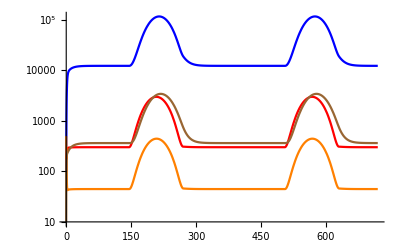

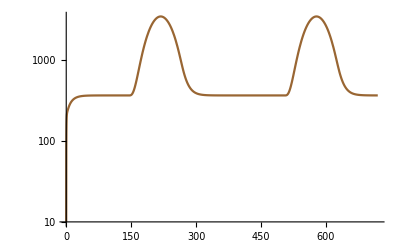

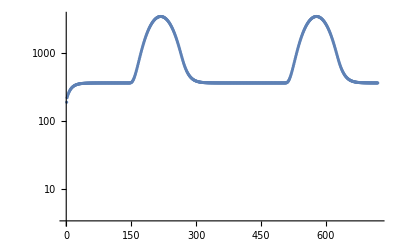

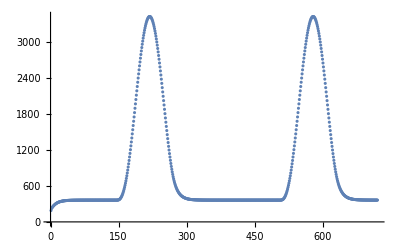

```mathematica
(* When there is no IRS then the mortality rate of adults is just the basline MuM0. This goes in the calculation of M'[t] *)

TimeMax=720;
β=21.19; (* Average number of eggs laid per day; value from Table 1*)
de=6.64; (* length of developmental period of eggs+early larvae in days; the reciprocal of dE is the rate of progression to the next stage; value from Table 1*)
dl=3.72; (* length of developmental period of late larvae in days; Instars that survive development will become pupae at a rate given by the reciprocal of dL; value from Table 1*)
dp=0.64; (*  length of developmental period of pupae, in days; Value from Table 1 *)
MuM0=0.096; (* Daily mortality rate of adult mosquitos; value from Table 1*)
MuP=0.25; (* The pupae daily mortality rate; value ftom Table 1*)
system = {
A'[t] == β* M[t]-A[t]/de-MuE [t]A[t], (*Eggs and early larvae stages*)
L'[t]==A[t]/de-L[t]/dl-MuL[t]*L[t],(*late larvae stages*)
P'[t]==L[t]/dl-P[t]/dp-MuP*P[t], (*Pupae*)
M'[t]==0.5*P[t]/dp-MuM0*M[t], (* Adult mosquitos, half of them are female *)
(* Initial conditions *)
M[0]==10,
A[0]==100,
P[0]==500,
L[0]==200
};
sol = NDSolve[system,{A[t],L[t],P[t],M[t]},{t,0,TimeMax}];
LogPlot[Evaluate[{A[t],L[t],P[t],M[t]}/.sol],{t,0,TimeMax}, PlotStyle->{Blue,Red,Orange,Brown, Purple}] (* Plot abundance of all stages *)
LogPlot[Evaluate[{M[t]}/.sol],{t,0,TimeMax}, PlotStyle->{Brown}] (* Plot abundance of adults *)
MosquitoNoIRS=Table[Evaluate[{M[t]}/.sol],{t,0,TimeMax}];

data=Transpose@{Range[0,TimeMax],Flatten[MosquitoNoIRS,2]};
data=Delete[data,1];
ListLogPlot[data, PlotRange->{0,Max[data]+1}]
ListPlot[data, PlotRange->{0,Max[data]+1}]
(*Export["~/Documents/malaria_interventions/mosquito_population_plosbiol_4.csv",data[[361;;720]]];*)
```

```mathematica
(*Typically the values would be FirstDayOfRain=160 & LastDayOfRain=270. For the PLOS Biol paper use FirstDayOfRain=145.*)
```

```mathematica
data[[361;;720]]
```

{{1,189.786},{2,221.458},{3,233.813},{4,244.237},{5,254.096},{6,263.328},{7,271.873},{8,279.736},{9,286.95},{10,293.559},{11,299.608},{12,305.143},{13,310.206},{14,314.835},{15,319.067},{16,322.935},{17,326.47},{18,329.7},{19,332.651},{20,335.347},{21,337.81},{22,340.06},{23,342.114},{24,343.991},{25,345.705},{26,347.27},{27,348.699},{28,350.003},{29,351.195},{30,352.283},{31,353.276},{32,354.183},{33,355.01},{34,355.766},{35,356.456},{36,357.086},{37,357.661},{38,358.186},{39,358.665},{40,359.102},{41,359.502},{42,359.866},{43,360.199},{44,360.503},{45,360.78},{46,361.033},{47,361.264},{48,361.475},{49,361.667},{50,361.843},{51,362.003},{52,362.15},{53,362.283},{54,362.405},{55,362.516},{56,362.618},{57,362.711},{58,362.795},{59,362.873},{60,362.943},{61,363.008},{62,363.066},{63,363.12},{64,363.169},{65,363.214},{66,363.254},{67,363.292},{68,363.326},{69,363.357},{70,363.385},{71,363.411},{72,363.434},{73,363.456},{74,363.475},{75,363.493},{76,363.51},{77,363.525},{78,363.538},{79,363.551},{80,363.562},{81,363.572},{82,363.582},{83,363.591},{84,363.598},{85,363.606},{86,363.612},{87,363.618},{88,363.624},{89,363.629},{90,363.633},{91,363.637},{92,363.641},{93,363.645},{94,363.648},{95,363.651},{96,363.653},{97,363.656},{98,363.658},{99,363.66},{100,363.662},{101,363.663},{102,363.665},{103,363.666},{104,363.668},{105,363.669},{106,363.67},{107,363.671},{108,363.672},{109,363.672},{110,363.673},{111,363.674},{112,363.674},{113,363.675},{114,363.676},{115,363.676},{116,363.676},{117,363.677},{118,363.677},{119,363.678},{120,363.678},{121,363.678},{122,363.678},{123,363.679},{124,363.679},{125,363.679},{126,363.679},{127,363.679},{128,363.679},{129,363.68},{130,363.68},{131,363.68},{132,363.68},{133,363.68},{134,363.68},{135,363.68},{136,363.68},{137,363.68},{138,363.68},{139,363.68},{140,363.68},{141,363.68},{142,363.68},{143,363.681},{144,363.681},{145,363.681},{146,363.693},{147,363.866},{148,364.494},{149,365.883},{150,368.315},{151,372.043},{152,377.291},{153,384.259},{154,393.121},{155,404.029},{156,417.115},{157,432.49},{158,450.252},{159,470.479},{160,493.238},{161,518.579},{162,546.542},{163,577.151},{164,610.419},{165,646.347},{166,684.922},{167,726.12},{168,769.905},{169,816.23},{170,865.035},{171,916.25},{172,969.793},{173,1025.57},{174,1083.49},{175,1143.42},{176,1205.26},{177,1268.88},{178,1334.13},{179,1400.89},{180,1468.98},{181,1538.27},{182,1608.6},{183,1679.79},{184,1751.67},{185,1824.09},{186,1896.85},{187,1969.79},{188,2042.73},{189,2115.49},{190,2187.88},{191,2259.73},{192,2330.86},{193,2401.1},{194,2470.26},{195,2538.17},{196,2604.67},{197,2669.59},{198,2732.76},{199,2794.03},{200,2853.24},{201,2910.23},{202,2964.88},{203,3017.03},{204,3066.56},{205,3113.34},{206,3157.26},{207,3198.19},{208,3236.05},{209,3270.73},{210,3302.14},{211,3330.21},{212,3354.86},{213,3376.04},{214,3393.68},{215,3407.75},{216,3418.2},{217,3425.01},{218,3428.17},{219,3427.67},{220,3423.5},{221,3415.68},{222,3404.23},{223,3389.18},{224,3370.56},{225,3348.42},{226,3322.82},{227,3293.83},{228,3261.51},{229,3225.95},{230,3187.25},{231,3145.49},{232,3100.78},{233,3053.25},{234,3003.},{235,2950.17},{236,2894.89},{237,2837.3},{238,2777.56},{239,2715.8},{240,2652.19},{241,2586.89},{242,2520.06},{243,2451.88},{244,2382.53},{245,2312.17},{246,2240.99},{247,2169.16},{248,2096.88},{249,2024.33},{250,1951.69},{251,1879.16},{252,1806.9},{253,1735.13},{254,1664.},{255,1593.72},{256,1524.46},{257,1456.4},{258,1389.72},{259,1324.58},{260,1261.17},{261,1199.64},{262,1140.16},{263,1082.87},{264,1027.94},{265,975.501},{266,925.692},{267,878.642},{268,834.474},{269,793.299},{270,755.223},{271,720.323},{272,688.517},{273,659.569},{274,633.227},{275,609.254},{276,587.435},{277,567.574},{278,549.494},{279,533.032},{280,518.043},{281,504.392},{282,491.958},{283,480.633},{284,470.315},{285,460.915},{286,452.349},{287,444.543},{288,437.429},{289,430.944},{290,425.033},{291,419.644},{292,414.731},{293,410.251},{294,406.167},{295,402.442},{296,399.044},{297,395.946},{298,393.12},{299,390.542},{300,388.191},{301,386.046},{302,384.089},{303,382.304},{304,380.675},{305,379.189},{306,377.834},{307,376.596},{308,375.468},{309,374.438},{310,373.498},{311,372.64},{312,371.857},{313,371.143},{314,370.491},{315,369.897},{316,369.354},{317,368.858},{318,368.406},{319,367.994},{320,367.617},{321,367.273},{322,366.96},{323,366.674},{324,366.412},{325,366.174},{326,365.956},{327,365.758},{328,365.576},{329,365.411},{330,365.26},{331,365.122},{332,364.996},{333,364.882},{334,364.777},{335,364.681},{336,364.594},{337,364.514},{338,364.441},{339,364.375},{340,364.314},{341,364.259},{342,364.209},{343,364.163},{344,364.121},{345,364.082},{346,364.047},{347,364.015},{348,363.986},{349,363.959},{350,363.935},{351,363.913},{352,363.893},{353,363.874},{354,363.857},{355,363.842},{356,363.828},{357,363.815},{358,363.803},{359,363.793},{360,363.783}}

## IRS SCHEME OF GHANA FIELD DATA (Used For PLOS Biology)

(*

The MuM function mimics the IRS applied in the field. IRS 1 had a coverage of 80%, IRS 2+3 had a coverage of 96%. To include the effect of the lifetime of the insecticides, and the fact that it takes time to spray all the compounds, we set the start time of the intervention to the middle time of the length it took to spray, and the total length of the intervention to the half-life of the insecticide. Specifically: 

IRS 1: Done between Oct-Dec 2013; We set starting date to Nov. 1st (running day 661). The intervention was with Organophosphates with lifetime of 2-3m. So we set the length to 75 days (661-735)
IRS 2: Done between May-Jul 2013; We set starting date to June 1st (running day 871). The intervention was with Organophosphates with lifetime of 2-3m. So we set the length to 75 days (871-945)
IRS 3: Done between Dec-Feb 2014; We set starting date to Jan 1st (running day 1081). The intervention was with 721+360 with lifetime of 4-6m. So we set the length to 150 days (1081-1231).

We let the model run for 5 years, to capture any effects of IRS on S5 and S6. We take the IRS data from day 661 because it takes one cycle (a year) to initiate the correct values (just like with the model without IRS, just seasonality)

*)

1800

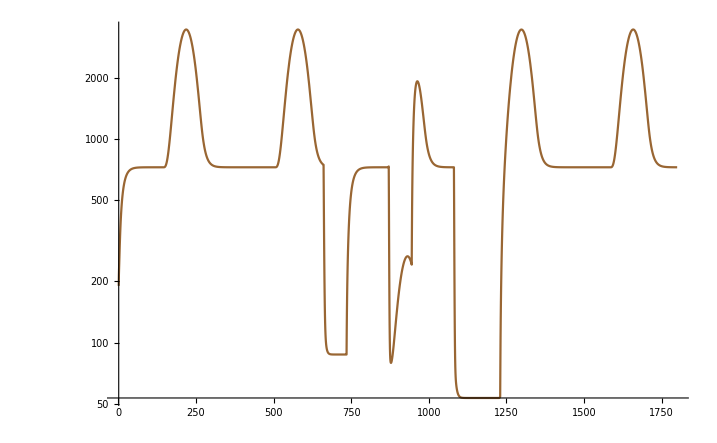

{{661,747.752},{662,436.224},{663,275.402},{664,191.86},{665,147.942},{666,124.369},{667,111.289},{668,103.683},{669,98.9969},{670,95.9322},{671,93.8184},{672,92.3},{673,91.1787},{674,90.3366},{675,89.6979},{676,89.2108},{677,88.8384},{678,88.5533},{679,88.3348},{680,88.1674},{681,88.039},{682,87.9406},{683,87.8652},{684,87.8073},{685,87.763},{686,87.729},{687,87.7029},{688,87.6829},{689,87.6676},{690,87.6558},{691,87.6468},{692,87.6399},{693,87.6346},{694,87.6306},{695,87.6274},{696,87.625},{697,87.6232},{698,87.6218},{699,87.6207},{700,87.6199},{701,87.6193},{702,87.6188},{703,87.6184},{704,87.6181},{705,87.6179},{706,87.6178},{707,87.6176},{708,87.6175},{709,87.6175},{710,87.6174},{711,87.6173},{712,87.6173},{713,87.6173},{714,87.6173},{715,87.6173},{716,87.6172},{717,87.6172},{718,87.6172},{719,87.6172},{720,87.6172},{721,87.6172},{722,87.6172},{723,87.6172},{724,87.6172},{725,87.6172},{726,87.6172},{727,87.6172},{728,87.6172},{729,87.6172},{730,87.6172},{731,87.6172},{732,87.6172},{733,87.6172},{734,87.6172},{735,87.6172},{736,135.052},{737,178.626},{738,219.477},{739,258.229},{740,294.972},{741,329.597},{742,362.005},{743,392.165},{744,420.112},{745,445.925},{746,469.71},{747,491.587},{748,511.682},{749,530.122},{750,547.029},{751,562.519},{752,576.706},{753,589.691},{754,601.574},{755,612.444},{756,622.384},{757,631.473},{758,639.782},{759,647.376},{760,654.316},{761,660.658},{762,666.451},{763,671.744},{764,676.579},{765,680.995},{766,685.029},{767,688.712},{768,692.076},{769,695.148},{770,697.953},{771,700.515},{772,702.853},{773,704.989},{774,706.938},{775,708.718},{776,710.343},{777,711.826},{778,713.181},{779,714.417},{780,715.546},{781,716.576},{782,717.517},{783,718.375},{784,719.159},{785,719.874},{786,720.527},{787,721.124},{788,721.668},{789,722.164},{790,722.618},{791,723.032},{792,723.409},{793,723.754},{794,724.069},{795,724.356},{796,724.618},{797,724.858},{798,725.076},{799,725.276},{800,725.458},{801,725.624},{802,725.775},{803,725.914},{804,726.04},{805,726.156},{806,726.261},{807,726.357},{808,726.445},{809,726.525},{810,726.598},{811,726.664},{812,726.725},{813,726.781},{814,726.831},{815,726.878},{816,726.92},{817,726.958},{818,726.994},{819,727.026},{820,727.055},{821,727.082},{822,727.106},{823,727.129},{824,727.149},{825,727.167},{826,727.184},{827,727.2},{828,727.214},{829,727.227},{830,727.239},{831,727.249},{832,727.259},{833,727.268},{834,727.276},{835,727.284},{836,727.291},{837,727.297},{838,727.302},{839,727.308},{840,727.312},{841,727.317},{842,727.321},{843,727.324},{844,727.327},{845,727.33},{846,727.333},{847,727.336},{848,727.338},{849,727.34},{850,727.342},{851,727.344},{852,727.345},{853,727.347},{854,727.348},{855,727.349},{856,727.35},{857,727.351},{858,727.352},{859,727.353},{860,727.354},{861,727.354},{862,727.355},{863,727.356},{864,727.356},{865,727.357},{866,727.368},{867,727.523},{868,728.083},{869,729.322},{870,731.494},{871,734.827},{872,320.754},{873,167.767},{874,111.317},{875,90.5148},{876,82.9125},{877,80.2909},{878,79.6807},{879,80.0293},{880,80.9686},{881,82.3651},{882,84.1618},{883,86.3243},{884,88.8252},{885,91.6395},{886,94.7439},{887,98.1166},{888,101.737},{889,105.586},{890,109.645},{891,113.896},{892,118.322},{893,122.905},{894,127.631},{895,132.481},{896,137.439},{897,142.489},{898,147.615},{899,152.8},{900,158.029},{901,163.284},{902,168.55},{903,173.812},{904,179.053},{905,184.258},{906,189.413},{907,194.502},{908,199.51},{909,204.424},{910,209.23},{911,213.914},{912,218.463},{913,222.865},{914,227.108},{915,231.18},{916,235.07},{917,238.768},{918,242.263},{919,245.547},{920,248.611},{921,251.446},{922,254.046},{923,256.403},{924,258.51},{925,260.364},{926,261.958},{927,263.288},{928,264.352},{929,265.146},{930,265.669},{931,265.918},{932,265.894},{933,265.596},{934,265.026},{935,264.184},{936,263.073},{937,261.696},{938,260.057},{939,258.159},{940,256.008},{941,253.609},{942,250.968},{943,248.093},{944,244.99},{945,241.668},{946,442.975},{947,624.982},{948,793.955},{949,952.892},{950,1101.31},{951,1237.66},{952,1360.78},{953,1470.21},{954,1566.04},{955,1648.71},{956,1718.84},{957,1777.17},{958,1824.49},{959,1861.58},{960,1889.22},{961,1908.17},{962,1919.14},{963,1922.84},{964,1919.92},{965,1911.},{966,1896.68},{967,1877.51},{968,1854.01},{969,1826.71},{970,1796.05},{971,1762.5},{972,1726.49},{973,1688.4},{974,1648.63},{975,1607.53},{976,1565.45},{977,1522.71},{978,1479.63},{979,1436.48},{980,1393.55},{981,1351.1},{982,1309.37},{983,1268.59},{984,1228.99},{985,1190.77},{986,1154.11},{987,1119.21},{988,1086.22},{989,1055.3},{990,1026.58},{991,1000.19},{992,976.104},{993,954.15},{994,934.148},{995,915.923},{996,899.316},{997,884.181},{998,870.386},{999,857.813},{1000,846.351},{1001,835.902},{1002,826.374},{1003,817.687},{1004,809.766},{1005,802.542},{1006,795.953},{1007,789.944},{1008,784.464},{1009,779.464},{1010,774.904},{1011,770.744},{1012,766.948},{1013,763.486},{1014,760.327},{1015,757.444},{1016,754.814},{1017,752.415},{1018,750.225},{1019,748.227},{1020,746.404},{1021,744.741},{1022,743.223},{1023,741.837},{1024,740.573},{1025,739.419},{1026,738.366},{1027,737.405},{1028,736.528},{1029,735.728},{1030,734.997},{1031,734.331},{1032,733.722},{1033,733.167},{1034,732.66},{1035,732.198},{1036,731.776},{1037,731.39},{1038,731.039},{1039,730.718},{1040,730.425},{1041,730.158},{1042,729.914},{1043,729.691},{1044,729.488},{1045,729.302},{1046,729.133},{1047,728.978},{1048,728.837},{1049,728.708},{1050,728.591},{1051,728.484},{1052,728.386},{1053,728.296},{1054,728.215},{1055,728.14},{1056,728.072},{1057,728.01},{1058,727.954},{1059,727.902},{1060,727.855},{1061,727.812},{1062,727.773},{1063,727.737},{1064,727.704},{1065,727.674},{1066,727.647},{1067,727.622},{1068,727.599},{1069,727.579},{1070,727.56},{1071,727.542},{1072,727.527},{1073,727.512},{1074,727.499},{1075,727.487},{1076,727.476},{1077,727.466},{1078,727.457},{1079,727.449},{1080,727.441},{1081,727.434},{1082,314.347},{1083,160.507},{1084,102.498},{1085,79.8623},{1086,70.3038},{1087,65.643},{1088,62.9031},{1089,61.0076},{1090,59.5618},{1091,58.4104},{1092,57.4802},{1093,56.7267},{1094,56.1173},{1095,55.6252},{1096,55.2286},{1097,54.9093},{1098,54.6526},{1099,54.4462},{1100,54.2803},{1101,54.1471},{1102,54.04},{1103,53.954},{1104,53.885},{1105,53.8295},{1106,53.785},{1107,53.7492},{1108,53.7205},{1109,53.6974},{1110,53.6789},{1111,53.664},{1112,53.6521},{1113,53.6425},{1114,53.6348},{1115,53.6286},{1116,53.6236},{1117,53.6196},{1118,53.6164},{1119,53.6138},{1120,53.6118},{1121,53.6101},{1122,53.6088},{1123,53.6077},{1124,53.6068},{1125,53.6061},{1126,53.6056},{1127,53.6051},{1128,53.6048},{1129,53.6045},{1130,53.6043},{1131,53.6041},{1132,53.6039},{1133,53.6038},{1134,53.6037},{1135,53.6036},{1136,53.6036},{1137,53.6035},{1138,53.6035},{1139,53.6035},{1140,53.6034},{1141,53.6034},{1142,53.6034},{1143,53.6034},{1144,53.6034},{1145,53.6034},{1146,53.6034},{1147,53.6033},{1148,53.6033},{1149,53.6033},{1150,53.6033},{1151,53.6033},{1152,53.6033},{1153,53.6033},{1154,53.6033},{1155,53.6033},{1156,53.6033},{1157,53.6033},{1158,53.6033},{1159,53.6033},{1160,53.6033},{1161,53.6033},{1162,53.6033},{1163,53.6033},{1164,53.6033},{1165,53.6033},{1166,53.6033},{1167,53.6033},{1168,53.6033},{1169,53.6033},{1170,53.6033},{1171,53.6033},{1172,53.6033},{1173,53.6033},{1174,53.6033},{1175,53.6033},{1176,53.6033},{1177,53.6033},{1178,53.6033},{1179,53.6033},{1180,53.6033},{1181,53.6033},{1182,53.6033},{1183,53.6033},{1184,53.6033},{1185,53.6033},{1186,53.6033},{1187,53.6033},{1188,53.6033},{1189,53.6033},{1190,53.6033},{1191,53.6033},{1192,53.6033},{1193,53.6033},{1194,53.6033},{1195,53.6033},{1196,53.6033},{1197,53.6033},{1198,53.6033},{1199,53.6033},{1200,53.6033},{1201,53.6033},{1202,53.6033},{1203,53.6033},{1204,53.6033},{1205,53.6033},{1206,53.6033},{1207,53.6033},{1208,53.6033},{1209,53.6033},{1210,53.6033},{1211,53.6033},{1212,53.6033},{1213,53.6033},{1214,53.6033},{1215,53.6033},{1216,53.6033},{1217,53.6033},{1218,53.6033},{1219,53.6033},{1220,53.6033},{1221,53.6033},{1222,53.6033},{1223,53.6033},{1224,53.6033},{1225,53.6033},{1226,53.6056},{1227,53.643},{1228,53.7809},{1229,54.0718},{1230,54.5457},{1231,102.079},{1232,146.978},{1233,191.21},{1234,236.061},{1235,281.822},{1236,328.303},{1237,375.262},{1238,422.552},{1239,470.135},{1240,518.043},{1241,566.356},{1242,615.175},{1243,664.61},{1244,714.768},{1245,765.749},{1246,817.643},{1247,870.523},{1248,924.45},{1249,979.467},{1250,1035.61},{1251,1092.88},{1252,1151.29},{1253,1210.82},{1254,1271.44},{1255,1333.12},{1256,1395.8},{1257,1459.42},{1258,1523.91},{1259,1589.18},{1260,1655.15},{1261,1721.72},{1262,1788.77},{1263,1856.21},{1264,1923.9},{1265,1991.73},{1266,2059.56},{1267,2127.27},{1268,2194.71},{1269,2261.76},{1270,2328.27},{1271,2394.11},{1272,2459.12},{1273,2523.16},{1274,2586.11},{1275,2647.8},{1276,2708.12},{1277,2766.91},{1278,2824.04},{1279,2879.39},{1280,2932.82},{1281,2984.2},{1282,3033.43},{1283,3080.37},{1284,3124.93},{1285,3166.99},{1286,3206.45},{1287,3243.23},{1288,3277.22},{1289,3308.36},{1290,3336.56},{1291,3361.76},{1292,3383.91},{1293,3402.93},{1294,3418.8},{1295,3431.47},{1296,3440.91},{1297,3447.11},{1298,3450.04},{1299,3449.71},{1300,3446.11},{1301,3439.26},{1302,3429.17},{1303,3415.88},{1304,3399.41},{1305,3379.81},{1306,3357.13},{1307,3331.43},{1308,3302.77},{1309,3271.24},{1310,3236.9},{1311,3199.85},{1312,3160.18},{1313,3118.},{1314,3073.41},{1315,3026.53},{1316,2977.47},{1317,2926.36},{1318,2873.34},{1319,2818.53},{1320,2762.08},{1321,2704.13},{1322,2644.82},{1323,2584.33},{1324,2522.78},{1325,2460.35},{1326,2397.2},{1327,2333.47},{1328,2269.35},{1329,2204.99},{1330,2140.56},{1331,2076.22},{1332,2012.14},{1333,1948.48},{1334,1885.41},{1335,1823.09},{1336,1761.68},{1337,1701.33},{1338,1642.21},{1339,1584.46},{1340,1528.24},{1341,1473.69},{1342,1420.95},{1343,1370.15},{1344,1321.43},{1345,1274.91},{1346,1230.7},{1347,1188.93},{1348,1149.69},{1349,1113.08},{1350,1079.2},{1351,1048.11},{1352,1019.75},{1353,993.905},{1354,970.364},{1355,948.92},{1356,929.382},{1357,911.58},{1358,895.358},{1359,880.574},{1360,867.099},{1361,854.816},{1362,843.619},{1363,833.411},{1364,824.103},{1365,815.616},{1366,807.877},{1367,800.819},{1368,794.382},{1369,788.512},{1370,783.157},{1371,778.272},{1372,773.816},{1373,769.751},{1374,766.043},{1375,762.66},{1376,759.573},{1377,756.757},{1378,754.187},{1379,751.843},{1380,749.703},{1381,747.751},{1382,745.969},{1383,744.344},{1384,742.86},{1385,741.507},{1386,740.271},{1387,739.144},{1388,738.115},{1389,737.176},{1390,736.319},{1391,735.537},{1392,734.823},{1393,734.172},{1394,733.577},{1395,733.035},{1396,732.539},{1397,732.087},{1398,731.675},{1399,731.298},{1400,730.955},{1401,730.641},{1402,730.355},{1403,730.094},{1404,729.855},{1405,729.638},{1406,729.439},{1407,729.258},{1408,729.092},{1409,728.941},{1410,728.803},{1411,728.678},{1412,728.563},{1413,728.458},{1414,728.362},{1415,728.275},{1416,728.195},{1417,728.123},{1418,728.056},{1419,727.996},{1420,727.94},{1421,727.89},{1422,727.844},{1423,727.802},{1424,727.763},{1425,727.728},{1426,727.696},{1427,727.667},{1428,727.64},{1429,727.616},{1430,727.594},{1431,727.574},{1432,727.555},{1433,727.538},{1434,727.523},{1435,727.509},{1436,727.496},{1437,727.484},{1438,727.474},{1439,727.464},{1440,727.455},{1441,727.447},{1442,727.439},{1443,727.433},{1444,727.426},{1445,727.421},{1446,727.416},{1447,727.411},{1448,727.407},{1449,727.403},{1450,727.399},{1451,727.396},{1452,727.393},{1453,727.39},{1454,727.388},{1455,727.385},{1456,727.383},{1457,727.381},{1458,727.38},{1459,727.378},{1460,727.377},{1461,727.375},{1462,727.374},{1463,727.373},{1464,727.372},{1465,727.371},{1466,727.37},{1467,727.37},{1468,727.369},{1469,727.368},{1470,727.368},{1471,727.367},{1472,727.367},{1473,727.366},{1474,727.366},{1475,727.366},{1476,727.365},{1477,727.365},{1478,727.365},{1479,727.364},{1480,727.364},{1481,727.364},{1482,727.364},{1483,727.364},{1484,727.363},{1485,727.363},{1486,727.363},{1487,727.363},{1488,727.363},{1489,727.363},{1490,727.363},{1491,727.363},{1492,727.363},{1493,727.362},{1494,727.362},{1495,727.362},{1496,727.362},{1497,727.362},{1498,727.362},{1499,727.362},{1500,727.362},{1501,727.362},{1502,727.362},{1503,727.362},{1504,727.362},{1505,727.362},{1506,727.362},{1507,727.362},{1508,727.362},{1509,727.362},{1510,727.362},{1511,727.362},{1512,727.362},{1513,727.362},{1514,727.362},{1515,727.362},{1516,727.362},{1517,727.362},{1518,727.362},{1519,727.362},{1520,727.362},{1521,727.362},{1522,727.362},{1523,727.362},{1524,727.362},{1525,727.362},{1526,727.362},{1527,727.362},{1528,727.362},{1529,727.362},{1530,727.362},{1531,727.362},{1532,727.362},{1533,727.362},{1534,727.362},{1535,727.362},{1536,727.362},{1537,727.362},{1538,727.362},{1539,727.362},{1540,727.362},{1541,727.362},{1542,727.362},{1543,727.362},{1544,727.362},{1545,727.362},{1546,727.362},{1547,727.362},{1548,727.362},{1549,727.362},{1550,727.362},{1551,727.362},{1552,727.362},{1553,727.362},{1554,727.362},{1555,727.362},{1556,727.362},{1557,727.362},{1558,727.362},{1559,727.362},{1560,727.362},{1561,727.362},{1562,727.362},{1563,727.362},{1564,727.362},{1565,727.362},{1566,727.362},{1567,727.362},{1568,727.362},{1569,727.362},{1570,727.362},{1571,727.362},{1572,727.362},{1573,727.362},{1574,727.362},{1575,727.362},{1576,727.362},{1577,727.362},{1578,727.362},{1579,727.362},{1580,727.362},{1581,727.362},{1582,727.362},{1583,727.362},{1584,727.362},{1585,727.362},{1586,727.372},{1587,727.527},{1588,728.086},{1589,729.325},{1590,731.497},{1591,734.83},{1592,739.531},{1593,745.78},{1594,753.737},{1595,763.543},{1596,775.318},{1597,789.165},{1598,805.169},{1599,823.403},{1600,843.92},{1601,866.764},{1602,891.963},{1603,919.533},{1604,949.479},{1605,981.795},{1606,1016.46},{1607,1053.45},{1608,1092.73},{1609,1134.24},{1610,1177.94},{1611,1223.74},{1612,1271.59},{1613,1321.39},{1614,1373.05},{1615,1426.47},{1616,1481.56},{1617,1538.19},{1618,1596.24},{1619,1655.59},{1620,1716.11},{1621,1777.66},{1622,1840.11},{1623,1903.3},{1624,1967.1},{1625,2031.34},{1626,2095.88},{1627,2160.56},{1628,2225.23},{1629,2289.73},{1630,2353.9},{1631,2417.58},{1632,2480.62},{1633,2542.85},{1634,2604.13},{1635,2664.31},{1636,2723.22},{1637,2780.73},{1638,2836.69},{1639,2890.96},{1640,2943.4},{1641,2993.89},{1642,3042.28},{1643,3088.47},{1644,3132.33},{1645,3173.75},{1646,3212.64},{1647,3248.88},{1648,3282.39},{1649,3313.08},{1650,3340.87},{1651,3365.7},{1652,3387.5},{1653,3406.22},{1654,3421.8},{1655,3434.21},{1656,3443.41},{1657,3449.39},{1658,3452.13},{1659,3451.61},{1660,3447.85},{1661,3440.84},{1662,3430.61},{1663,3417.19},{1664,3400.61},{1665,3380.9},{1666,3358.13},{1667,3332.34},{1668,3303.6},{1669,3271.99},{1670,3237.59},{1671,3200.48},{1672,3160.76},{1673,3118.53},{1674,3073.89},{1675,3026.96},{1676,2977.87},{1677,2926.72},{1678,2873.66},{1679,2818.83},{1680,2762.35},{1681,2704.37},{1682,2645.05},{1683,2584.53},{1684,2522.97},{1685,2460.52},{1686,2397.35},{1687,2333.62},{1688,2269.48},{1689,2205.11},{1690,2140.67},{1691,2076.32},{1692,2012.23},{1693,1948.56},{1694,1885.48},{1695,1823.15},{1696,1761.74},{1697,1701.39},{1698,1642.26},{1699,1584.51},{1700,1528.29},{1701,1473.73},{1702,1420.98},{1703,1370.18},{1704,1321.46},{1705,1274.93},{1706,1230.73},{1707,1188.95},{1708,1149.71},{1709,1113.1},{1710,1079.22},{1711,1048.13},{1712,1019.76},{1713,993.917},{1714,970.376},{1715,948.93},{1716,929.392},{1717,911.589},{1718,895.366},{1719,880.581},{1720,867.105},{1721,854.822},{1722,843.624},{1723,833.415},{1724,824.108},{1725,815.62},{1726,807.881},{1727,800.823},{1728,794.385},{1729,788.514},{1730,783.159},{1731,778.274},{1732,773.818},{1733,769.753},{1734,766.045},{1735,762.661},{1736,759.575},{1737,756.758},{1738,754.188},{1739,751.844},{1740,749.704},{1741,747.752},{1742,745.97},{1743,744.345},{1744,742.861},{1745,741.507},{1746,740.272},{1747,739.144},{1748,738.115},{1749,737.176},{1750,736.319},{1751,735.537},{1752,734.824},{1753,734.172},{1754,733.578},{1755,733.035},{1756,732.54},{1757,732.088},{1758,731.675},{1759,731.299},{1760,730.955},{1761,730.641},{1762,730.355},{1763,730.094},{1764,729.855},{1765,729.638},{1766,729.439},{1767,729.258},{1768,729.092},{1769,728.941},{1770,728.803},{1771,728.678},{1772,728.563},{1773,728.458},{1774,728.362},{1775,728.275},{1776,728.195},{1777,728.123},{1778,728.056},{1779,727.996},{1780,727.94},{1781,727.89},{1782,727.844},{1783,727.802},{1784,727.763},{1785,727.728},{1786,727.696},{1787,727.667},{1788,727.64},{1789,727.616},{1790,727.594},{1791,727.574},{1792,727.555},{1793,727.538},{1794,727.523},{1795,727.509},{1796,727.496},{1797,727.484},{1798,727.474},{1799,727.464},{1800,727.455}}

~/Documents/malaria_interventions/IRS_Ghana.csv

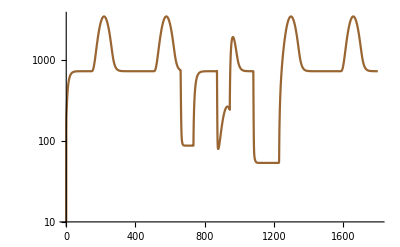

1801

{{360,727.455},{361,727.447},{362,727.439},{363,727.433},{364,727.426},{365,727.421},{366,727.416},{367,727.411},{368,727.407},{369,727.403},{370,727.399},{371,727.396},{372,727.393},{373,727.39},{374,727.388},{375,727.385},{376,727.383},{377,727.381},{378,727.38},{379,727.378},{380,727.377},{381,727.375},{382,727.374},{383,727.373},{384,727.372},{385,727.371},{386,727.37},{387,727.37},{388,727.369},{389,727.368},{390,727.368},{391,727.367},{392,727.367},{393,727.366},{394,727.366},{395,727.366},{396,727.365},{397,727.365},{398,727.365},{399,727.364},{400,727.364},{401,727.364},{402,727.364},{403,727.364},{404,727.363},{405,727.363},{406,727.363},{407,727.363},{408,727.363},{409,727.363},{410,727.363},{411,727.363},{412,727.363},{413,727.362},{414,727.362},{415,727.362},{416,727.362},{417,727.362},{418,727.362},{419,727.362},{420,727.362},{421,727.362},{422,727.362},{423,727.362},{424,727.362},{425,727.362},{426,727.362},{427,727.362},{428,727.362},{429,727.362},{430,727.362},{431,727.362},{432,727.362},{433,727.362},{434,727.362},{435,727.362},{436,727.362},{437,727.362},{438,727.362},{439,727.362},{440,727.362},{441,727.362},{442,727.362},{443,727.362},{444,727.362},{445,727.362},{446,727.362},{447,727.362},{448,727.362},{449,727.362},{450,727.362},{451,727.362},{452,727.362},{453,727.362},{454,727.362},{455,727.362},{456,727.362},{457,727.362},{458,727.362},{459,727.362},{460,727.362},{461,727.362},{462,727.362},{463,727.362},{464,727.362},{465,727.362},{466,727.362},{467,727.362},{468,727.362},{469,727.362},{470,727.362},{471,727.362},{472,727.362},{473,727.362},{474,727.362},{475,727.362},{476,727.362},{477,727.362},{478,727.362},{479,727.362},{480,727.362},{481,727.362},{482,727.362},{483,727.362},{484,727.362},{485,727.362},{486,727.362},{487,727.362},{488,727.362},{489,727.362},{490,727.362},{491,727.362},{492,727.362},{493,727.362},{494,727.362},{495,727.362},{496,727.362},{497,727.362},{498,727.362},{499,727.362},{500,727.362},{501,727.362},{502,727.362},{503,727.362},{504,727.362},{505,727.362},{506,727.372},{507,727.527},{508,728.086},{509,729.325},{510,731.497},{511,734.83},{512,739.531},{513,745.78},{514,753.737},{515,763.543},{516,775.318},{517,789.165},{518,805.169},{519,823.403},{520,843.92},{521,866.764},{522,891.963},{523,919.533},{524,949.479},{525,981.795},{526,1016.46},{527,1053.45},{528,1092.73},{529,1134.24},{530,1177.94},{531,1223.74},{532,1271.59},{533,1321.39},{534,1373.05},{535,1426.47},{536,1481.56},{537,1538.19},{538,1596.24},{539,1655.59},{540,1716.11},{541,1777.66},{542,1840.11},{543,1903.3},{544,1967.1},{545,2031.34},{546,2095.88},{547,2160.56},{548,2225.23},{549,2289.73},{550,2353.9},{551,2417.58},{552,2480.62},{553,2542.85},{554,2604.13},{555,2664.31},{556,2723.22},{557,2780.73},{558,2836.69},{559,2890.96},{560,2943.4},{561,2993.89},{562,3042.28},{563,3088.47},{564,3132.33},{565,3173.75},{566,3212.64},{567,3248.88},{568,3282.39},{569,3313.08},{570,3340.87},{571,3365.7},{572,3387.5},{573,3406.22},{574,3421.8},{575,3434.21},{576,3443.41},{577,3449.39},{578,3452.13},{579,3451.61},{580,3447.85},{581,3440.84},{582,3430.61},{583,3417.19},{584,3400.61},{585,3380.9},{586,3358.13},{587,3332.34},{588,3303.6},{589,3271.99},{590,3237.59},{591,3200.48},{592,3160.76},{593,3118.53},{594,3073.89},{595,3026.96},{596,2977.87},{597,2926.72},{598,2873.66},{599,2818.83},{600,2762.35},{601,2704.37},{602,2645.05},{603,2584.53},{604,2522.97},{605,2460.52},{606,2397.35},{607,2333.62},{608,2269.48},{609,2205.11},{610,2140.67},{611,2076.32},{612,2012.23},{613,1948.56},{614,1885.48},{615,1823.15},{616,1761.74},{617,1701.39},{618,1642.26},{619,1584.51},{620,1528.29},{621,1473.73},{622,1420.98},{623,1370.18},{624,1321.46},{625,1274.93},{626,1230.73},{627,1188.95},{628,1149.71},{629,1113.1},{630,1079.22},{631,1048.13},{632,1019.76},{633,993.917},{634,970.376},{635,948.93},{636,929.392},{637,911.589},{638,895.366},{639,880.581},{640,867.105},{641,854.822},{642,843.624},{643,833.415},{644,824.108},{645,815.62},{646,807.881},{647,800.823},{648,794.385},{649,788.514},{650,783.159},{651,778.274},{652,773.818},{653,769.753},{654,766.045},{655,762.661},{656,759.575},{657,756.758},{658,754.188},{659,751.844},{660,749.704},{661,747.752},{662,436.224},{663,275.402},{664,191.86},{665,147.942},{666,124.369},{667,111.289},{668,103.683},{669,98.9969},{670,95.9322},{671,93.8184},{672,92.3},{673,91.1787},{674,90.3366},{675,89.6979},{676,89.2108},{677,88.8384},{678,88.5533},{679,88.3348},{680,88.1674},{681,88.039},{682,87.9406},{683,87.8652},{684,87.8073},{685,87.763},{686,87.729},{687,87.7029},{688,87.6829},{689,87.6676},{690,87.6558},{691,87.6468},{692,87.6399},{693,87.6346},{694,87.6306},{695,87.6274},{696,87.625},{697,87.6232},{698,87.6218},{699,87.6207},{700,87.6199},{701,87.6193},{702,87.6188},{703,87.6184},{704,87.6181},{705,87.6179},{706,87.6178},{707,87.6176},{708,87.6175},{709,87.6175},{710,87.6174},{711,87.6173},{712,87.6173},{713,87.6173},{714,87.6173},{715,87.6173},{716,87.6172},{717,87.6172},{718,87.6172},{719,87.6172},{720,87.6172},{721,87.6172},{722,87.6172},{723,87.6172},{724,87.6172},{725,87.6172},{726,87.6172},{727,87.6172},{728,87.6172},{729,87.6172},{730,87.6172},{731,87.6172},{732,87.6172},{733,87.6172},{734,87.6172},{735,87.6172},{736,135.052},{737,178.626},{738,219.477},{739,258.229},{740,294.972},{741,329.597},{742,362.005},{743,392.165},{744,420.112},{745,445.925},{746,469.71},{747,491.587},{748,511.682},{749,530.122},{750,547.029},{751,562.519},{752,576.706},{753,589.691},{754,601.574},{755,612.444},{756,622.384},{757,631.473},{758,639.782},{759,647.376},{760,654.316},{761,660.658},{762,666.451},{763,671.744},{764,676.579},{765,680.995},{766,685.029},{767,688.712},{768,692.076},{769,695.148},{770,697.953},{771,700.515},{772,702.853},{773,704.989},{774,706.938},{775,708.718},{776,710.343},{777,711.826},{778,713.181},{779,714.417},{780,715.546},{781,716.576},{782,717.517},{783,718.375},{784,719.159},{785,719.874},{786,720.527},{787,721.124},{788,721.668},{789,722.164},{790,722.618},{791,723.032},{792,723.409},{793,723.754},{794,724.069},{795,724.356},{796,724.618},{797,724.858},{798,725.076},{799,725.276},{800,725.458},{801,725.624},{802,725.775},{803,725.914},{804,726.04},{805,726.156},{806,726.261},{807,726.357},{808,726.445},{809,726.525},{810,726.598},{811,726.664},{812,726.725},{813,726.781},{814,726.831},{815,726.878},{816,726.92},{817,726.958},{818,726.994},{819,727.026},{820,727.055},{821,727.082},{822,727.106},{823,727.129},{824,727.149},{825,727.167},{826,727.184},{827,727.2},{828,727.214},{829,727.227},{830,727.239},{831,727.249},{832,727.259},{833,727.268},{834,727.276},{835,727.284},{836,727.291},{837,727.297},{838,727.302},{839,727.308},{840,727.312},{841,727.317},{842,727.321},{843,727.324},{844,727.327},{845,727.33},{846,727.333},{847,727.336},{848,727.338},{849,727.34},{850,727.342},{851,727.344},{852,727.345},{853,727.347},{854,727.348},{855,727.349},{856,727.35},{857,727.351},{858,727.352},{859,727.353},{860,727.354},{861,727.354},{862,727.355},{863,727.356},{864,727.356},{865,727.357},{866,727.368},{867,727.523},{868,728.083},{869,729.322},{870,731.494},{871,734.827},{872,320.754},{873,167.767},{874,111.317},{875,90.5148},{876,82.9125},{877,80.2909},{878,79.6807},{879,80.0293},{880,80.9686},{881,82.3651},{882,84.1618},{883,86.3243},{884,88.8252},{885,91.6395},{886,94.7439},{887,98.1166},{888,101.737},{889,105.586},{890,109.645},{891,113.896},{892,118.322},{893,122.905},{894,127.631},{895,132.481},{896,137.439},{897,142.489},{898,147.615},{899,152.8},{900,158.029},{901,163.284},{902,168.55},{903,173.812},{904,179.053},{905,184.258},{906,189.413},{907,194.502},{908,199.51},{909,204.424},{910,209.23},{911,213.914},{912,218.463},{913,222.865},{914,227.108},{915,231.18},{916,235.07},{917,238.768},{918,242.263},{919,245.547},{920,248.611},{921,251.446},{922,254.046},{923,256.403},{924,258.51},{925,260.364},{926,261.958},{927,263.288},{928,264.352},{929,265.146},{930,265.669},{931,265.918},{932,265.894},{933,265.596},{934,265.026},{935,264.184},{936,263.073},{937,261.696},{938,260.057},{939,258.159},{940,256.008},{941,253.609},{942,250.968},{943,248.093},{944,244.99},{945,241.668},{946,442.975},{947,624.982},{948,793.955},{949,952.892},{950,1101.31},{951,1237.66},{952,1360.78},{953,1470.21},{954,1566.04},{955,1648.71},{956,1718.84},{957,1777.17},{958,1824.49},{959,1861.58},{960,1889.22},{961,1908.17},{962,1919.14},{963,1922.84},{964,1919.92},{965,1911.},{966,1896.68},{967,1877.51},{968,1854.01},{969,1826.71},{970,1796.05},{971,1762.5},{972,1726.49},{973,1688.4},{974,1648.63},{975,1607.53},{976,1565.45},{977,1522.71},{978,1479.63},{979,1436.48},{980,1393.55},{981,1351.1},{982,1309.37},{983,1268.59},{984,1228.99},{985,1190.77},{986,1154.11},{987,1119.21},{988,1086.22},{989,1055.3},{990,1026.58},{991,1000.19},{992,976.104},{993,954.15},{994,934.148},{995,915.923},{996,899.316},{997,884.181},{998,870.386},{999,857.813},{1000,846.351},{1001,835.902},{1002,826.374},{1003,817.687},{1004,809.766},{1005,802.542},{1006,795.953},{1007,789.944},{1008,784.464},{1009,779.464},{1010,774.904},{1011,770.744},{1012,766.948},{1013,763.486},{1014,760.327},{1015,757.444},{1016,754.814},{1017,752.415},{1018,750.225},{1019,748.227},{1020,746.404},{1021,744.741},{1022,743.223},{1023,741.837},{1024,740.573},{1025,739.419},{1026,738.366},{1027,737.405},{1028,736.528},{1029,735.728},{1030,734.997},{1031,734.331},{1032,733.722},{1033,733.167},{1034,732.66},{1035,732.198},{1036,731.776},{1037,731.39},{1038,731.039},{1039,730.718},{1040,730.425},{1041,730.158},{1042,729.914},{1043,729.691},{1044,729.488},{1045,729.302},{1046,729.133},{1047,728.978},{1048,728.837},{1049,728.708},{1050,728.591},{1051,728.484},{1052,728.386},{1053,728.296},{1054,728.215},{1055,728.14},{1056,728.072},{1057,728.01},{1058,727.954},{1059,727.902},{1060,727.855},{1061,727.812},{1062,727.773},{1063,727.737},{1064,727.704},{1065,727.674},{1066,727.647},{1067,727.622},{1068,727.599},{1069,727.579},{1070,727.56},{1071,727.542},{1072,727.527},{1073,727.512},{1074,727.499},{1075,727.487},{1076,727.476},{1077,727.466},{1078,727.457},{1079,727.449},{1080,727.441}}

```mathematica
MuM [c1_,c2_,Q_,ϕ_,r_,ψ_,t_]:= Piecewise[{{-Log[0.91*w[c1,Q,ϕ,r,ψ]*0.74/1-Q *c* ϕ* r*0.74]/3,301+360<=t<=375+360},{-Log[0.91*w[c2,Q,ϕ,r,ψ]*0.74/1-Q *c* ϕ* r*0.74]/3,511+360<=t≤585+360||721+360<=t<870+360}},MuM0]; 
(*Table[MuM[0.8,0.96,0.92,0.97,0.207,0.86,t],{t,1,1440}]*)
TimeMax=5*360;
β=21.19; (* Average number of eggs laid per day; value from Table 1*)
de=6.64; (* length of developmental period of eggs+early larvae in days; the reciprocal of dE is the rate of progression to the next stage; value from Table 1*)
dl=3.72; (* length of developmental period of late larvae in days; Instars that survive development will become pupae at a rate given by the reciprocal of dL; value from Table 1*)
dp=0.64; (*  length of developmental period of pupae, in days; Value from Table 1 *)
MuM0=0.096; (* Daily mortality rate of adult mosquitos; value from Table 1*)
MuP=0.25; (* The pupae daily mortality rate; value ftom Table 1*)
system = {
A'[t] == β* M[t]-A[t]/de-MuE [t]A[t], (*Eggs and early larvae stages*)
L'[t]==A[t]/de-L[t]/dl-MuL[t]*L[t],(*late larvae stages*)
P'[t]==L[t]/dl-P[t]/dp-MuP*P[t], (*Pupae*)
M'[t]==0.5*P[t]/dp-MuM[0.8,0.96,0.92,0.97,0.207,0.86,t]*M[t], (* Adult mosquitos, half of them are female *)
(* Initial conditions *)
M[0]==10,
A[0]==100,
P[0]==500,
L[0]==200
};
sol = NDSolve[system,{A[t],L[t],P[t],M[t]},{t,1,TimeMax}];
(*LogPlot[Evaluate[{A[t],L[t],P[t],M[t]}/.sol],{t,0,TimeMax}, PlotStyle->{Blue,Red,Orange,Brown, Purple}] (* Plot abundance of all stages *) *)

MosquitoIRS=Table[Evaluate[{M[t]}/.sol],{t,1,TimeMax}];
data=Transpose@{Range[1,TimeMax],Flatten[MosquitoIRS,2]};
Length[data]
LogPlot[Evaluate[{M[t]}/.sol],{t,1,TimeMax}, PlotStyle->{Brown}] (* Plot abundance of adults *)
data[[661;;TimeMax]]
Export["~/Documents/malaria_interventions/IRS_Ghana.csv",data[[661;;TimeMax]]]
```

## Mosquito population dynamics with IRS

```mathematica
(* Need to set the IRS scheme, so change these next three lines as necessary, see the examples above *)
w[c_,Q_,ϕ_,r_,ψ_]:=1-Q*c*ϕ*(1-(1-r)(1-ψ)); (* A function indicating how IRS cahnges the adult mortatlity rate. c is coverge and it is the only parameter here we should change. Parameters and their values are taken from Table S3 in the supplementary information *)
FirstDay=120;
LastDay=300;
TimeMax=2*360;
c=0.9;

generateIRS[FirstDay_, LastDay_, TimeMax_, coverage_] := {

filename="~/Documents/malaria_interventions_data/IRS_"<>ToString[FirstDay]<>"_"<>ToString[LastDay]<>"_"<>ToString[coverage]<>"_"<>ToString[TimeMax]<>".csv";
MuM [c_,Q_,ϕ_,r_,ψ_,t_]:= Piecewise[{{-Log[0.91*w[c,Q,ϕ,r,ψ]*0.74/1-Q *c* ϕ* r*0.74]/3,FirstDay<Mod[t,360]<LastDay}},MuM0];

β=21.19; (* Average number of eggs laid per day; value from Table 1*)
de=6.64; (* length of developmental period of eggs+early larvae in days; the reciprocal of dE is the rate of progression to the next stage; value from Table 1*)
dl=3.72; (* length of developmental period of late larvae in days; Instars that survive development will become pupae at a rate given by the reciprocal of dL; value from Table 1*)
     dp=0.64; (*  length of developmental period of pupae, in days; Value from Table 1 *)
MuM0=0.096; (* Daily mortality rate of adult mosquitos; value from Table 1*)
MuP=0.25; (* The pupae daily mortality rate; value ftom Table 1*)
system = {
A'[t] == β* M[t]-A[t]/de-MuE [t]A[t], (*Eggs and early larvae stages*)
L'[t]==A[t]/de-L[t]/dl-MuL[t]*L[t],(*late larvae stages*)
P'[t]==L[t]/dl-P[t]/dp-MuP*P[t], (*Pupae*)
M'[t]==0.5*P[t]/dp-MuM[coverage,0.92,0.97,0.207,0.86,t]*M[t], (*Adult mosquitos, half of them are female*)
(* Initial conditions *)
M[0]==10,
A[0]==100,
P[0]==500,
L[0]==200
};
sol = NDSolve[system,{A[t],L[t],P[t],M[t]},{t,0,TimeMax}];
LogPlot[Evaluate[{A[t],L[t],P[t],M[t]}/.sol],{t,0,TimeMax}, PlotStyle->{Blue,Red,Orange,Brown}]; (* Plot abundance of all stages *)
LogPlot[Evaluate[{M[t]}/.sol],{t,0,TimeMax}, PlotStyle->{Brown}]; (* Plot abundance of adults *)
MosquitoIRS=Table[Evaluate[{M[t]}/.sol],{t,0,TimeMax}];(* Obtain mosquito abundance with intervention*)

data=Transpose@{Range[0,TimeMax],Flatten[MosquitoIRS,2]};
data=Delete[data,1];
Export[filename,data];
data
}
```

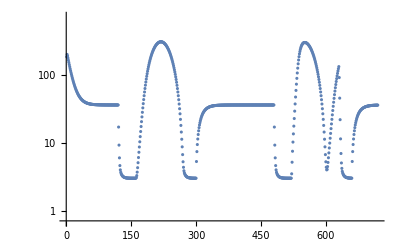

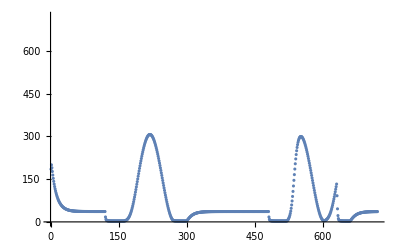

```mathematica
d=generateIRS[120,300,2*360,0.9];
ListLogPlot[d, PlotRange->{0,Max[d]+1}]
ListPlot[d, PlotRange->{0,Max[d]+1}]
```

```mathematica
LengthRange=360*Range[5,20,5];
CoverageRange=Range[0.8,1,0.05];
Table[generateIRS[120,300,a,b],{a,LengthRange},{b,CoverageRange}];
```

```mathematica
5
```